```mathematica
f=Function[{R,J},({{0, 1}, {-1, 0}}).{R,J}]
```

Function[{R,J},{{0,1},{-1,0}}.{R,J}]

```mathematica
f[1,0]
```

{0,-1}

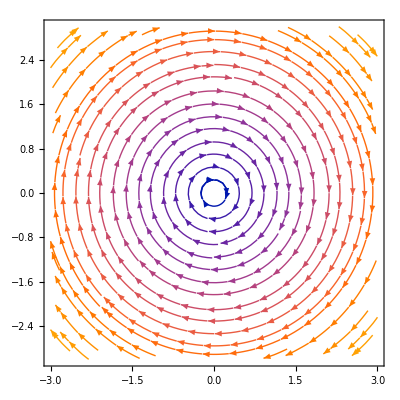

```mathematica
StreamPlot[f[R,J],{R,-3,3},{J,-3,3}]
```

```mathematica
update=Function[{x},x+0.001f[x[[1]],x[[2]]]]
```

Function[{x},x+0.001 f[x⟦1⟧,x⟦2⟧]]

```mathematica
update[{1,0}]
update[{1,-0.1}]
update[{0.99,-0.2}]
```

{1.,-0.001}

{0.9999,-0.101}

{0.9898,-0.20099}

(1 | 0
1. | -0.001
0.999999 | -0.002
0.999997 | -0.003
0.999994 | -0.004)

(1 | 1. | 0.999999 | 0.999997 | 0.999994
0 | -0.001 | -0.002 | -0.003 | -0.004)

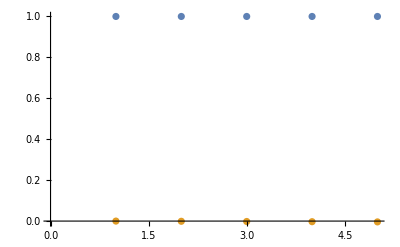

```mathematica
NestList[update,{1,0},4]//MatrixForm
{Map[First,%],Map[Function[v,v[[2]]],%]}//MatrixForm
ListPlot[%]
```

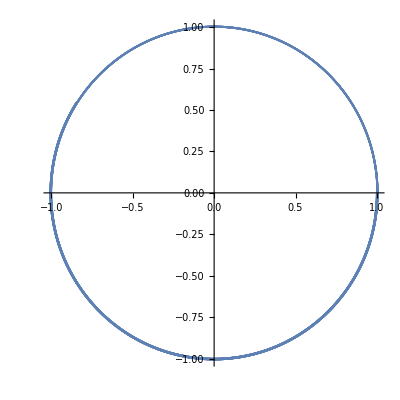

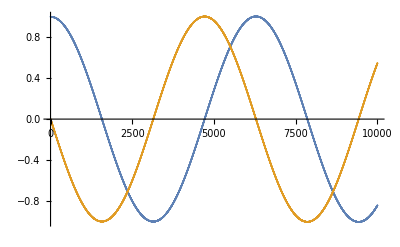

```mathematica
NestList[update,{1,0},10000];
ListPlot[%,AspectRatio->1]
ListPlot[Transpose[%%]]
```